```mathematica
(* Infinitesimal generator of diffusion Y *)
```

```mathematica
A[f_]:=Subscript[μ, Y][y] D[f,y]+1/2 D[f,{y,2}]
```

```mathematica
(* OU process*)
```

```mathematica
A[f_]:=-y  D[f,y]+1/2 D[f,{y,2}]
```

```mathematica
(* A[f_]:=D[μ,{y,0}] D[f,y]+1/2 D[f,{y,2}] *)
```

```mathematica
Hermite[j_,x_]:=(-1)^j 2^(-j/2)HermiteH[j,x/(√2)]
```

```mathematica
(* Approximation of E[Subscript[H, j](Δ^(-1/2)(Subscript[Y, t+Δ]-Subscript[y, 0]))|Subscript[Y, t]=Subscript[y, 0]; θ]
For a fixed J, expands up to order K in Δ. Recommended that K = J/2 *)
```

```mathematica
(*given j, how far do I need to go?*)
```

```mathematica
c[j_,k_]:=Δ^k/(k!)Nest[A,Hermite[j,Δ^(-1/2)(y-y0)],k]/.y -> y0
```

```mathematica
(* while loop test*)
```

```mathematica
Subscript[η, Z][j_,K_]:=
Block[{u=0, i =1,maxp = 0},
If[j === 0,Return[1]];
s = Hermite[j,Δ^(-1/2)(y-y0)]/.y -> y0;
While[(Max@Cases[s,Power[_,Δ_?NumberQ] :> Δ, -1] ≤ K) &&(maxp ≤ K),
expr = Collect[c[j,i],Δ];
list =
Which[Head[expr] ===Integer,{Coefficient[#,Δ,Exponent[#,Δ]],#,Exponent[#,Δ]}&/@  List @ expr,
	  Head[expr] ===Times, List[{Coefficient[#,Δ,Exponent[#,Δ]],#,Exponent[#,Δ]}& @  expr],
	  Head[expr] ===Plus, {Coefficient[#,Δ,Exponent[#,Δ]],#,Exponent[#,Δ]}&/@( List@@  expr )
];
maxp = Max@Cases[expr,Power[_,Δ_?NumberQ] :> Δ, -1];
filter = Position[Last /@ list, _?(#  <=  K &)] // Flatten;
filteredlist = list[[filter]];
s = s+ ∑_(k=1)^Length[filteredlist] filteredlist[[k,1]] Δ^filteredlist[[k,3]];
i = i+ 1
];
Return[Collect[s/(j!),Δ,Simplify]]
]
```

```mathematica
Table[Subscript[η, Z][j,3],{j,0,3}]
```

{1,y0 √Δ-1/2 y0 Δ^(3/2)+1/6 y0 Δ^(5/2),1/2 (-1+y0^2) Δ+1/6 (2-3 y0^2) Δ^2+1/24 (-4+7 y0^2) Δ^3,1/6 y0 (-3+y0^2) Δ^(3/2)+1/12 (7 y0-3 y0^3) Δ^(5/2)}

```mathematica
Subscript[η, Z][6,3]
```

1/48 (-5+9 y0^2-y0^4) Δ^2+1/192 (-4+7 y0^2) Δ^3

```mathematica
Subscript[p, Z][z_,J_,K_]:=1/(√(2π))ⅇ^(-z^2/2)∑_(j=0)^J Subscript[η, Z][j,K]Hermite[j,z]
```

```mathematica
Subscript[p, Y][y_,K_]:=1/(√Δ)Subscript[p, Z][Δ^(-1/2)(y- y0),2K,K]
```

```mathematica
Subscript[p, Y][z,1]
```

(ⅇ^(-(-y0+z)^2/(2 Δ)) (1-y0 (-y0+z)+1/4 (-1+y0^2) (-2+(2 (-y0+z)^2)/Δ) Δ))/(√(2 π) √Δ)

```mathematica
Subscript[p, Z][z,4,2]/. y0 -> 0/. Δ-> 0.3//FullSimplify
```

ⅇ^(-z^2/2) (0.46028-0.0748017 z^2+0.0044881 z^4)

```mathematica
Subscript[p, Y][y,4,2]/. y0 -> 0/. Δ-> 0.3//FullSimplify
```

ⅇ^(-1.66667 y^2) (0.840352-0.455229 y^2+0.0910457 y^4)

```mathematica
(*Exact transition density of OU*)
```

```mathematica
t[x_,y_,b_,a_,t_,σ_]:=
PDF[NormalDistribution[a + (x-a)ⅇ^(-b t),√(σ^2(1-Exp[-2b t])/(2 b))],y]
```

```mathematica
(*Euler approximation transition density*)
```

```mathematica
ϕ[x_,y_,dt_]:= PDF[NormalDistribution[x-x dt, √dt ],y]
```

```mathematica
(*plot compare*)
```

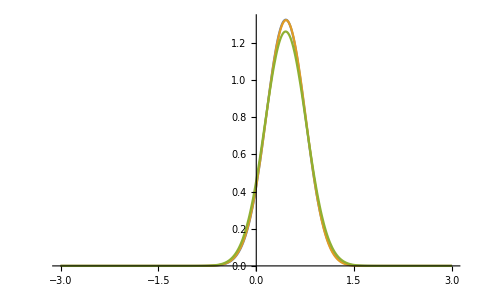

```mathematica
Plot[{t[0.5,z,1,0,0.1,1],Subscript[p, Y][z,1]/. y0 -> 0.5/. Δ-> 0.1,ϕ[0.5,z,0.1]},{z,-3,3},PlotRange->Full]
```

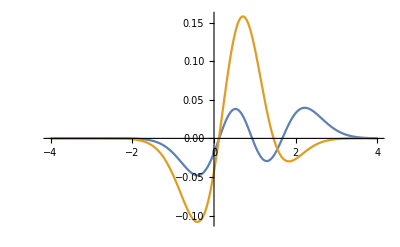

```mathematica
Plot[{t[1,z,1,0,0.5,1] - (Subscript[p, Y][z,1]/. y0 -> 1/. Δ-> 0.5),t[1,z,1,0,0.5,1] -ϕ[1,z,0.5]},{z,-4,4},PlotRange->Full
]
```

```mathematica
Manipulate[Plot[{t[0,z,1,0,dt,1],Subscript[p, Y][z,4,2]/. y0 -> 0/. Δ-> dt,ϕ[0,z,dt]},{z,-3,3},PlotLegends->"Expressions"],{dt,0.01,1,0.2}]
```

```mathematica
f[x_,y_]:=x +y
```

(x+y)[(x+y)[(x+y)[x]]]

```mathematica
B[μ_,f_]:=D[μ,{y,0}] D[f,y]+1/2 D[f,{y,2}]
```

```mathematica
D[B[√y,√y],y]
```

3/(16 y^(5/2))

```mathematica
B[√y]
```

√y[y]

```mathematica
√x'//FullForm
```

Derivative[1][Power[x,Rational[1,2]]]

```mathematica
Subscript[p, Z][z,y0,6,3]
```

1/(√(2 π))ⅇ^(-z^2/2) (1-1/96 (12-24 z^2+4 z^4) Δ^2 (6 μ_Y[y0]^2 μ_Y'[y0]+4 μ_Y'[y0]^2+7 μ_Y[y0] μ_Y''[y0]+2 μ_Y^(3)[y0])+1/768 (-120+360 z^2-120 z^4+8 z^6) Δ (-6 μ_Y'[y0]+4 Δ μ_Y'[y0]^2+6 μ_Y[y0]^2 (-1+Δ μ_Y'[y0])+7 Δ μ_Y[y0] μ_Y''[y0]+2 Δ μ_Y^(3)[y0])+1/24 (-2+2 z^2) Δ (6 μ_Y'[y0]+4 Δ μ_Y'[y0]^2+6 μ_Y[y0]^2 (1+Δ μ_Y'[y0])+7 Δ μ_Y[y0] μ_Y''[y0]+2 Δ μ_Y^(3)[y0])+1/(768 √2)(60 √2 z-40 √2 z^3+4 √2 z^5) Δ^(3/2) (-16 μ_Y[y0]^3+4 Δ μ_Y[y0]^2 μ_Y''[y0]+(-22+6 Δ μ_Y'[y0]) μ_Y''[y0]+4 μ_Y[y0] (μ_Y'[y0] (-15+Δ μ_Y'[y0])+Δ μ_Y^(3)[y0])+Δ μ_Y^(4)[y0])-1/(96 √2)(-6 √2 z+2 √2 z^3) Δ^(3/2) (-8 μ_Y[y0]^3+4 Δ μ_Y[y0]^2 μ_Y''[y0]+(-8+6 Δ μ_Y'[y0]) μ_Y''[y0]+4 μ_Y[y0] (μ_Y'[y0] (-6+Δ μ_Y'[y0])+Δ μ_Y^(3)[y0])+Δ μ_Y^(4)[y0])+1/24 z √Δ (4 Δ^2 μ_Y[y0]^2 μ_Y''[y0]+4 μ_Y[y0] (6+Δ (μ_Y'[y0] (3+Δ μ_Y'[y0])+Δ μ_Y^(3)[y0]))+Δ (6 (1+Δ μ_Y'[y0]) μ_Y''[y0]+Δ μ_Y^(4)[y0])))